```mathematica
Clear["Global`*"]
(*name="student@10.0.1.9://home/student/BEM/Kramer2021_0d03/result.json"*)
data01DLPF4=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/LPF4/01D_LPF4.txt"}],"Data"];
data03DLPF4=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/LPF4/03D_LPF4.txt"}],"Data"];
%[[1]]
data01DFNPF1=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/FNPF1/01D_FNPF1.txt"}],"Data"];
data03DFNPF1=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/FNPF1/03D_FNPF1.txt"}],"Data"];
%[[1]]
data01DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/01D_CI95_Normalized.txt"}],"Data"];
%[[1]]
data03DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/03D_CI95_Normalized.txt"}],"Data"];
%[[1]]
data05DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/05D_Measured1_Normalized.txt"}],"Data"];
%[[1]]
name="/Users/tomoaki/BEM/Kramer2021_H00d03_small_meshC_ALE1_0d5/result.json"

Quiet[Z=(data="float_COM"/.Import[name])[[;;,3]];];
Quiet[Vx=(data="float_velocity"/.Import[name])[[;;,1]];];
Quiet[Vy=(data="float_velocity"/.Import[name])[[;;,2]];];
Quiet[Vz=(data="float_velocity"/.Import[name])[[;;,3]];];
Quiet[time="simulation_time"/.Import[name];];
(*Kramer20210d03=Import[NotebookDirectory[]<>"Kramer2021_0d3.csv"];*)
H0=30/1000;
jsonInfo[imported_]:=Grid[Join[{{"no.","title","data length"}},Table[{i,imported[[i]][[1]],Length[imported[[i]][[2]]]},{i,1,Min[10,Length[imported]]}]],Frame->All,Background->{None,{LightGray,{LightMagenta,Magenta}}}];
jsonInfo[Import[name,"JSON"]]
```

{t [s],,x3 [m]}

{t [s],,x3 [m]}

{t/Te0 [-],,x3/H_{0,m} (mean) [-],,Lower 95% CI bound [-],,Upper 95% CI bound [-]}

{t/Te0 [-],,x3/H_{0,m} (mean) [-],,Lower 95% CI bound [-],,Upper 95% CI bound [-]}

{t/Te0 [-],,x3/H_{0,m} [-],,WG1/H_{0,m} [-],,WG2/H_{0,m} [-],,WG3/H_{0,m} [-]}

/Users/tomoaki/BEM/Kramer2021_H00d03_small_meshC_ALE1_0d5/result.json

no. | title | data length
1 | cpu_time | 2749
2 | float_COM | 2749
3 | float_EK | 2749
4 | float_EP | 2749
5 | float_accel | 2749
6 | float_area | 2749
7 | float_force | 2749
8 | float_pitch | 2749
9 | float_roll | 2749
10 | float_torque | 2749

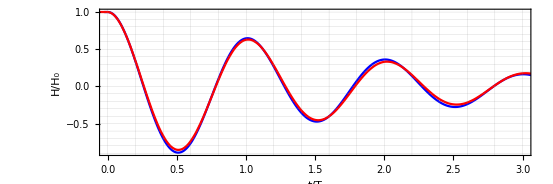

```mathematica
opt={FrameStyle->Directive[FontSize->16,Black,Thickness[0.002]],
GridLines->All,
GridLinesStyle->Directive[Gray,AbsoluteThickness[0.001]],
ImageSize->400,
PlotStyle->{{Blue},{Red}},
AspectRatio->1/3};
plotxrange={1,13};

T=0.76;
fig=ListPlot[
{(*{#1/T,#2/H0}&@@@data01DLPF4[[2;;]],
{#1/T,#2/H0}&@@@data01DFNPF1[[2;;]],*)
{(time-0.02)/T,(Z-((*-34.8+*)900)/1000)/H0}ᵀ,
{#1,#2(*/H0*)}&@@@data01DMeasured1Raw[[2;;]]
(*,{#1/0.76,#2/H0}&@@@data01DFNPF1[[2;;]]
,{#1/0.76,#2/H0}&@@@data01DLPF4[[2;;]]*)

},
Joined->{True,True},
BaseStyle->{FontFamily->"Times"},
PlotRange->{{0,3.},All},
Evaluate[opt],
Frame->True,
FrameLabel->{Style["t/T",FontSize->16,FontFamily->"Times",Italic],Style["H/H_0",FontSize->16,FontFamily->"Times",Italic]}
(*FrameStyle->Directive[FontSize->16,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],*)
(*PlotLegends->Placed[LineLegend[{"Experimental Results (Kramer et al., 2021)","BEM"},LegendMarkerSize->20,LabelStyle->15],{0.65,0.15}]*)
]
```

```mathematica
(*dir="/Users/tomoaki/Library/CloudStorage/Dropbox/meeting/海洋工学シンポジウム/2023/投稿論文/"*)
dir=NotebookDirectory[];
r=200
Export[dir<>"HH0_vs_tT_Kramer2012.jpg",fig,ImageResolution->r];
Export[dir<>"HH0_vs_tT_Kramer2012.png",fig,ImageResolution->r];
Export[dir<>"HH0_vs_tT_Kramer2012.pdf",fig];
Export[dir<>"HH0_vs_tT_Kramer2012.eps",fig];
Export[dir<>"HH0_vs_tT_Kramer2012.jpeg",fig,ImageResolution->r];
```

200

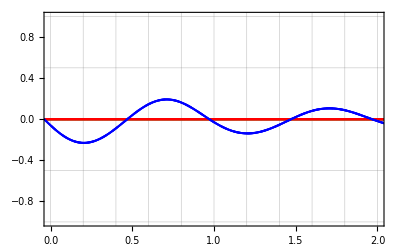

```mathematica
ListPlot[
{
{(time-0.05)/0.76,Vx}ᵀ,
{(time-0.05)/0.76,Vy}ᵀ,
{(time-0.05)/0.76,Vz}ᵀ
},
PlotStyle->{{Darker[Green],Opacity[0.6]},{Red},{Dashed,Blue,Opacity[0.6]},{Thick}},
Joined->{False,True,True,True},
PlotRange->{{0,2},{-1.,1.}},
PlotTheme->"Scientific",
Frame->True,
Mesh->All,
GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]}
]
```